```mathematica
hedge=Flatten[Import["c:\\book1.txt","Table"],1];
```

```mathematica
Length[hedge]
```

892

```mathematica
g=FinancialData["DAX","1.1.2000"];
```

```mathematica
dax=Transpose[g][[2]][[1;;Length[hedge]]];
```

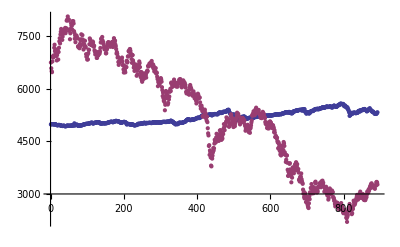

```mathematica
ListPlot[{hedge,dax}]
```

```mathematica
hedge=Log[hedge];dax=Log[dax];
```

```mathematica
hedge=Differences[hedge];
```

```mathematica
dax=Differences[dax];
```

```mathematica
w=Transpose[{hedge,dax}];
```

```mathematica
w=Sort[w,#1[[1]]<#2[[1]]&];
```

```mathematica
hedge=Transpose[w][[1]];
dax=Transpose[w][[2]];
```

```mathematica
w[[2]]
```

{-0.0117745,0.0306036}

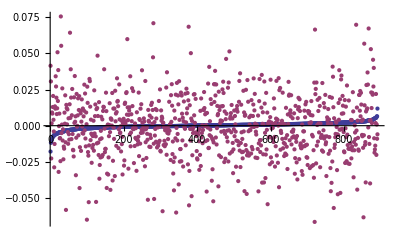

```mathematica
ListPlot[Transpose[w],PlotRange->All]
```

```mathematica
nN=20;wN=Length[hedge];
m0=Min[Transpose[w][[1]]]
Max[Transpose[w][[1]]]
m1=Min[Transpose[w][[2]]]
Max[Transpose[w][[2]]]
f0=(nN-1)/(Max[Transpose[w][[1]]]-m0)
f1=(nN-1)/(Max[Transpose[w][[2]]]-m1)
d=1/wN//N
```

-0.0178719

0.0118256

-0.0665223

0.0755268

639.785

133.757

0.00112233

```mathematica
F={};For[i=1,i≤wN,i++,
For[j=1,j≤wN,j++,
m=0;
If[w[[j,1]]<=w[[i,1]]  && w[[j,2]]≤w[[i,2]],m++;];
];
AppendTo[F,{w[[i,1]],w[[i,2]],m/wN}];
]
```

$Aborted

```mathematica
U={};nN=20;For[i=0,i≤nN,i++,
AppendTo[U,{min0,i/nN*(max1-min1)+min1,0}];
]
For[i=0,i≤nN,i++,
AppendTo[U,{i/nN*(max0-min0)+min0,min1,0}];
]
For[i=0,i≤nN,i++,
AppendTo[U,{max0,i/nN*(max1-min1)+min1,Length[Select[w,#[[1]]<=max0  && #[[2]]<=i/nN*(max1-min1)+min1&]]/wN}];
]
For[i=0,i≤nN,i++,
AppendTo[U,{i/nN*(max0-min0)+min0,max1,Length[Select[w,#[[2]]<=max1  && #[[1]]<=i/nN*(max0-min0)+min0&]]/wN}];
]
```

```mathematica
wN=Length[hedge];
min0=Min[Transpose[w][[1]]];
max0=Max[Transpose[w][[1]]];
min1=Min[Transpose[w][[2]]];
max1=Max[Transpose[w][[2]]];
```

```mathematica
U={};sdax=Sort[dax];AppendTo[U,{max0,max1,1}];

For[i=1,i≤wN,i++,
//AppendTo[U,{hedge[[i]],max1,(i-1)/wN}];
AppendTo[U,{max0,sdax[[i]],(i-1)/wN}];
AppendTo[U,{min0,sdax[[i]],0}];
]
```

```mathematica
F={};For[i=1,i≤wN,i++,
AppendTo[F,{w[[i,1]],w[[i,2]],Length[Select[w,#[[1]]<w[[i,1]]  && #[[2]]<w[[i,2]]&]]/wN}];
]
```

```mathematica
W=Join[F,U];
```

```mathematica
ListPointPlot3D[W]
```

-Graphics3D-

```mathematica
ww={};
For[i=1,i≤wN,i++,
AppendTo[ww,Select[W,#[[2]]==sdax[[i]]&]];
]
```

```mathematica
Length[W]
Length[Flatten[ww,1]]
```

3565

0

```mathematica
ww[[1]]
```

{{-0.0178719,0.041439,0},{-0.0178719,0.0755268,0},{-0.0178719,-0.0665223,0}}

```mathematica
ListPointPlot3D[Flatten[ww,1]]
```

-Graphics3D-

```mathematica
Po[a_,b_]:=If[b==0,1,If[b==-1,0,a^b]];
```

```mathematica
B[n_,i_,x_]:=Binomial[n,i] Po[x,i] Po[1-x,n-i];
```

```mathematica
nn=Length[ww]
```

891

```mathematica
f[a_,b_]:=Sum[B[nn,i,a]Sum[ww[[i+1,j+1]]B[Length[ww[[j]]],j,b],{j,0,Length[ww[[j]]]-1}]//N,{i,0,nn-1}]
```

```mathematica
f[0,0]
```

{-0.0178719,0.041439,0.}

```mathematica
nnn=10;pl=Flatten[Table[f[i/nnn,j/nnn],{i,0,nnn},{j,0,nnn}],1];
```

```mathematica
pll=Select[pl,Head[#]==Head[{0.,0.,0.}]&];
```

```mathematica
ListPointPlot3D[pll]
```

-Graphics3D-

```mathematica
Select[W,#[[1]]==hedge[[3]]&]
```

{{-0.0114726,-0.0226471,0},{-0.0114726,0.0755268,2/891}}

```mathematica
ListPointPlot3D[Select[W,#[[1]]==hedge[[3]]&]]
```

-Graphics3D-

```mathematica
w[[2]]
```

```mathematica
Length[Flatten[w,1]]
```

891

```mathematica
Length[W]
```

4455

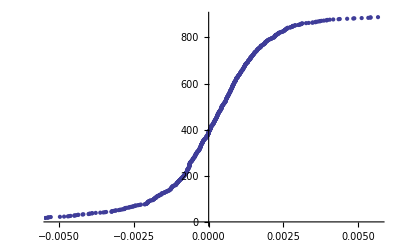

```mathematica
ListPlot[hrand]
```

```mathematica
nn=Length[hedge]
```

891

```mathematica
F[[1,1]]
```

{-0.0665223,-0.0178719,0}

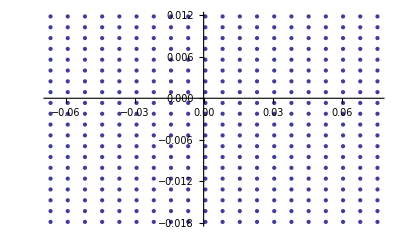

```mathematica
ListPlot[Transpose[Transpose[Q][[1;;2]]]]
```

```mathematica
w[[1]]
```

{0.041439,-0.0178719}

```mathematica
F=Table[{m0+i/f0,m1+j/f1,0},{i,0,nN-1},{j,0,nN-1}];For[i=1,i≤nN,i++,
For[j=1,j≤nN,j++,
For[k=1,k≤wN,k++,
If[w[[k,2]]≤F[[i,j,2]] &&w[[k,1]]≤F[[i,j,1]] ,F[[i,j,3]]+=d;];
]
]];Q=Flatten[F,1];
```

```mathematica
ListPointPlot3D[Q]
```

-Graphics3D-

```mathematica
w=Import["c:\\Trivariat.txt","Table"];
```

```mathematica
Length[w]
```

216000

```mathematica
Length[w]^(1/3)
```

60

```mathematica
w[[8000]]
```

{-0.016865,-0.035223,-0.008308,0.}

```mathematica
w1=Select[w,#[[1]]==w[[1000,1]]&];
```

```mathematica
fif=Transpose[Transpose[w1][[2;;4]]];
```

```mathematica
ListPointPlot3D[fif]
```

-Graphics3D-

```mathematica
u=60;
```

```mathematica
fi={};For[i=0,i<u,i++,
AppendTo[fi,fif[[i*u+1;;(i+1) *u]]];
]
```

```mathematica
fif[[21;;40]]
```

{{-0.059046,-0.017872,0.},{-0.059046,-0.016309,0.},{-0.059046,-0.014746,0.},{-0.059046,-0.013183,0.},{-0.059046,-0.01162,0.},{-0.059046,-0.010057,0.},{-0.059046,-0.008494,0.},{-0.059046,-0.006931,0.},{-0.059046,-0.005368,0.},{-0.059046,-0.003805,0.},{-0.059046,-0.002242,0.},{-0.059046,-0.000679,0.},{-0.059046,0.000884,0.},{-0.059046,0.002447,0.},{-0.059046,0.00401,0.},{-0.059046,0.005573,0.},{-0.059046,0.007136,0.},{-0.059046,0.0087,0.},{-0.059046,0.010263,0.},{-0.059046,0.011826,0.}}

```mathematica
fi[[1,13]]
```

{-0.066522,-0.011832,0.}

```mathematica
Po[a_,b_]:=If[b==0,1,If[b==-1,0,a^b]];
```

```mathematica
nn=Length[fi]
```

60

```mathematica
bi=Table[Binomial[nn-1,i],{i,0,nn-1}];
```

```mathematica
B[n_,i_,x_]:=bi[[i+1]] Po[x,i] Po[1-x,n-1-i];
```

```mathematica
f[a_,b_]:=Sum[B[nn,i,a]B[nn,j,b]fi[[i+1,j+1]],{i,0,nn-1},{j,0,nn-1}];
```

```mathematica
f[0.1,0.1]
```

{-0.0523174,-0.0149022,3.53251×10^-36}

```mathematica
an=15;tt=Table[f[i/an,j/an],{i,0,an},{j,0,an}];
```

```mathematica
tt=Flatten[tt,1];
```

```mathematica
ListPointPlot3D[fif,PlotStyle->Red]
```

-Graphics3D-

```mathematica
Show[ListPointPlot3D[fif,PlotStyle->Red],ListPlot3D[tt]]
```

-Graphics3D-

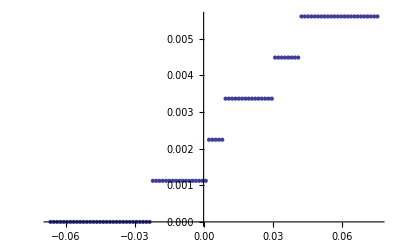

```mathematica
p=3000;ListPlot[{#[[2]],#[[3]]}&/@Select[w,#[[1]]==w[[p,1]]&]]
```

```mathematica
ll={#[[2]],#[[3]]}&/@Select[w,#[[1]]==w[[p,1]]&];
```

```mathematica
ListPlot[ll]
```

-Graphics-

```mathematica
Max[Table[w[[k,3]]-Q[[k,3]],{k,nN^2}]]
```

4.74747×10^-7